## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
data=Import["junk.csv"];
```

```mathematica
Take[data,5]
```

{{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{area-of-circle,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0,1},{bernoulli,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0,0,1},{combo-magnification,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{compo-general-case,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,0,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
logistic[n_,{nl_,b_}]:=1/(Exp[-b (n-nl)]+1);
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl]+1) (1-ps-pg)/2;
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b n]
```

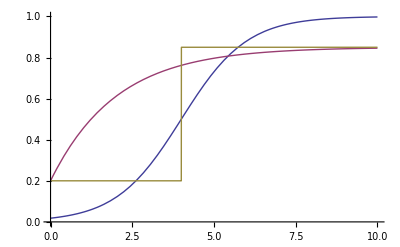

```mathematica
Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,0,10},PlotRange->{0,1}]
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[logger[If[data[[i]]==1,model[i,params],1-model[i,params]],params],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Map[{#[[1]],Which[Length[Drop[#,3]]<Length[vars],Null,Length[Drop[#,3]]==Length[vars],2 Length[vars],True,Block[{x=NMaximize[{logProb[model,vars,Drop[#,3]],constraints[Drop[#,3]]},vars,Method->{"RandomSearch",Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[#,x];False]]]}&,data]
```

```mathematica
data[[29]]
```

{define-image-distance,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,1,0,1}

```mathematica
logProb[logistic,{-8.7,30},Drop[data[[9]],3]]
```

-3.×10^50

```mathematica
TableForm[maxer[logistic,{nl,b},(nl≥-10 Length[#]&& nl≤11 Length[#]&& b>-5Length[#] && b<5Length[#])&,data[[{9}]]]]
```

compo-z-axis | 16.8925

```mathematica
1
```

```mathematica
TableForm[maxer[logistic,{nl,b},(nl≥-10 Length[#]&& nl≤ 11 Length[#]&& b>-10 Length[#] && b<10 Length[#])&,data]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
TableForm[maxer[bkt,{b,pg,ps},pg≥0 && ps≥0 && pg≤1 && ps≤ 1 &&b≥0,Take[data,20]]]
```

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 6
combo-magnification | Null
compo-general-case | 35.8378
compo-general-case-unknown | Null
compo-parallel-axis | 85.444
compo-perpendicular | 42.5766
compo-z-axis | 18.3684
compo-zero-vector | Null

```mathematica
TableForm[maxer[step,{nl,pg,ps},pg≥0 && ps≥0 && pg≤1 && ps≤1 &&Element[nl,Integers]&&nl≥0,Take[data,20]]]
```

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 6
combo-magnification | Null
compo-general-case | 34.6219
compo-general-case-unknown | Null
compo-parallel-axis | 84.7132
compo-perpendicular | 40.7894
compo-z-axis | 16.9895
compo-zero-vector | Null